```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h,k]
```

```mathematica
(*Qudratic Sawtooth (cartoon) function*)
f[x_]:=x^2/;0<=x<=1/2
f[x_]:=0.5-x^2/3-0.169/;1/2<x≤1
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

f[Mod[Abs[x],1]]

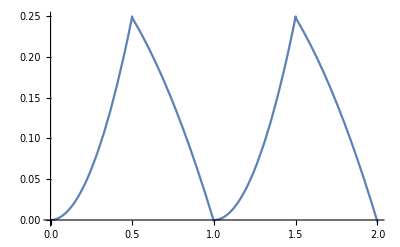

```mathematica
Plot[f[Mod[Abs[x],1]],{x,0,2}]
```

```mathematica
s0=Log[2]/Log[3]
```

Log[2]/Log[3]

```mathematica
hh[x_]=Sum[ff[3^k*x]/3^(s0*k),{k,0,20}];
```

```mathematica
kk[x_]=Sum[ff[3^k*(x-1/2)]/3^(s0*k),{k,0,20}];
```

```mathematica
a=ParallelTable[{kk[n/30000],hh[n/30000]},{n,1,30000}];
```

```mathematica
b=ParallelTable[{-kk[n/30000],hh[n/30000]},{n,1,30000}];
```

```mathematica
c=ParallelTable[{kk[n/30000],-hh[n/30000]},{n,1,30000}];
```

```mathematica
d=ParallelTable[-{kk[n/30000],hh[n/30000]},{n,1,30000}];
```

```mathematica
ga=Show[Graphics[{Red,PointSize[0.003],Point/@a,Blue,PointSize[0.003],Point/@b,Cyan,PointSize[0.003],Point/@c,Magenta,PointSize[0.003],Point/@d}],Axes->False,ImageSize->2000];
```

```mathematica
Export["Biscuit_Sawtooth_quadrant30000.jpg",ga]
```

Biscuit_Sawtooth_quadrant30000.jpg

```mathematica
(*end*)
```